### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,3,S1},{1,2,4,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.042101 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j481==0&&jt494==0&&u503==2&&u504==1&&-2≤u505≤1
and the rules are:
<|j484→1,u512→0,u513→1,j479→1,j480→1-j481,j482→1-j481,j483→j481,j485→0,j486→0,j487→0,j488→0,j489→0,j490→0,jt491→0,jt492→1,jt493→1-jt494,jt495→-j481+jt494,jt496→j481-jt494,jt497→j481-jt494,jt498→-j481+jt494,jt499→1-j481,jt500→0,jt501→j481,jt502→0,u506→0,u507→1,u509→-1+u503,u510→-1+j481+u504,u511→-j481+u505,u514→u503,u508→u503|>

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{-2≤u505≤1,<|j484→1,u512→0,u513→1,j479→1,j480→1-0,j482→1-0,j483→0,j485→0,j486→0,j487→0,j488→0,j489→0,j490→0,jt491→0,jt492→1,jt493→1-0,jt495→-0+0,jt496→0-0,jt497→0-0,jt498→-0+0,jt499→1-0,jt500→0,jt501→0,jt502→0,u506→0,u507→1,u509→-1+2,u510→-1+0+1,u511→-0+u505,u514→2,u508→2,j481→0,jt494→0,u503→2,u504→1|>}

DataToEquations: There are multiple solutions for the given data.

DataToEquations: Done.

{0.061934,Null}

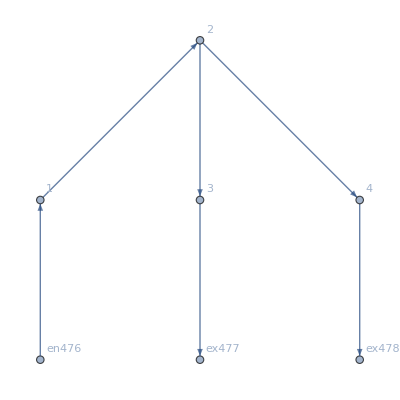

current: <|{1,1->2}→0,{1,en476->1}→1,{2,1->2}→1,{2,2->3}→0,{2,2->4}→0,{3,2->3}→1,{3,3->ex477}→0,{4,2->4}→0,{4,4->ex478}→0,{en476,en476->1}→0,{ex477,3->ex477}→1,{ex478,4->ex478}→0|>

transition: <|{1,1->2,en476->1}→0,{1,en476->1,1->2}→1,{2,1->2,2->3}→1,{2,1->2,2->4}→0,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,2->3,3->ex477}→1,{3,3->ex477,2->3}→0,{4,2->4,4->ex478}→0,{4,4->ex478,2->4}→0|>

value: <|{1,1->2}→2,{1,en476->1}→2,{2,1->2}→1,{2,2->3}→1,{2,2->4}→u505,{3,2->3}→0,{3,3->ex477}→0,{4,2->4}→u505,{4,4->ex478}→1,{en476,en476->1}→2,{ex477,3->ex477}→0,{ex478,4->ex478}→1|>

```mathematica
(MFGEquations=DataToEquations[Data/.{I1->1,U1->(*at vertex 3*)0,U2->(*at vertex 4*)1(*, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1*),S1->(*S124*)0,S2->(*S123*)3,S3->3,S4->3,S5->0,S6->0}];)//Timing
If[MFGEquations =!= Null,
Print[MFGEquations["FG"]];
Print["current: ", MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort];
Print["transition: ", MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort];
Print["value: ", MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
]
```

#### In the next example, it looks like we may choose one of the values for the value function. One of the extremes should be the consistent choice.

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->(*at vertex 3*)0,U2->(*at vertex 4*)31,S1->1,S2->4,S3->3,S4->5,S5->3,S6->0}];//Timing
Print["current: ", MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["transition: ", MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["value: ", MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
```

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.041915 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j520==0&&jt533==0&&u542==3&&u543==1&&-2≤u544≤1
and the rules are:
<|j523→1,u551→0,u552→31,j518→1,j519→1-j520,j521→1-j520,j522→j520,j524→0,j525→0,j526→0,j527→0,j528→0,j529→0,jt530→0,jt531→1,jt532→1-jt533,jt534→-j520+jt533,jt535→j520-jt533,jt536→j520-jt533,jt537→-j520+jt533,jt538→1-j520,jt539→0,jt540→j520,jt541→0,u545→0,u546→31,u548→-1+u542,u549→-1+j520+u543,u550→-j520+u544,u553→u542,u547→u542|>

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{-2≤u544≤1,<|j523→1,u551→0,u552→31,j518→1,j519→1-0,j521→1-0,j522→0,j524→0,j525→0,j526→0,j527→0,j528→0,j529→0,jt530→0,jt531→1,jt532→1-0,jt534→-0+0,jt535→0-0,jt536→0-0,jt537→-0+0,jt538→1-0,jt539→0,jt540→0,jt541→0,u545→0,u546→31,u548→-1+3,u549→-1+0+1,u550→-0+u544,u553→3,u547→3,j520→0,jt533→0,u542→3,u543→1|>}

DataToEquations: There are multiple solutions for the given data.

DataToEquations: Done.

{0.060737,Null}

current: <|{1,1->2}→0,{1,en515->1}→1,{2,1->2}→1,{2,2->3}→0,{2,2->4}→0,{3,2->3}→1,{3,3->ex516}→0,{4,2->4}→0,{4,4->ex517}→0,{en515,en515->1}→0,{ex516,3->ex516}→1,{ex517,4->ex517}→0|>

transition: <|{1,1->2,en515->1}→0,{1,en515->1,1->2}→1,{2,1->2,2->3}→1,{2,1->2,2->4}→0,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,2->3,3->ex516}→1,{3,3->ex516,2->3}→0,{4,2->4,4->ex517}→0,{4,4->ex517,2->4}→0|>

value: <|{1,1->2}→3,{1,en515->1}→3,{2,1->2}→2,{2,2->3}→1,{2,2->4}→u544,{3,2->3}→0,{3,3->ex516}→0,{4,2->4}→u544,{4,4->ex517}→31,{en515,en515->1}→3,{ex516,3->ex516}→0,{ex517,4->ex517}→31|>

```mathematica
Prin
```

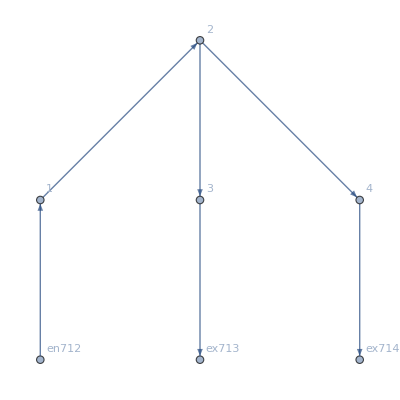

```mathematica
MFGEquations["FG"]
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.88178×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.88178×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→11.4115,u312→0.705756,u313→0.705756,u314→0,u315→31,u316→11.4115,u317→10.7058,u318→0.,u319→0.705756,u320→0,u321→31,u322→11.4115|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.11022×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.11022×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→11.4537,u312→0.72685,u313→0.72685,u314→0,u315→31,u316→11.4537,u317→10.7268,u318→0.,u319→0.72685,u320→0,u321→31,u322→11.4537|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.55112×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.55112×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→11.5464,u312→0.773209,u313→0.773209,u314→0,u315→31,u316→11.5464,u317→10.7732,u318→0.,u319→0.773209,u320→0,u321→31,u322→11.5464|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.66134×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.66134×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→11.9184,u312→0.959201,u313→0.959201,u314→0,u315→31,u316→11.9184,u317→10.9592,u318→0.,u319→0.959201,u320→0,u321→31,u322→11.9184|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.57009×10^-15,ComplexInfinity]

<|j287→1,j288→1,j289→0,j290→1,j291→0,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1,jt302→0,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1,jt308→0,jt309→0,jt310→0,u311→12,u312→1,u313→1,u314→0,u315→31,u316→12,u317→11,u318→0,u319→1,u320→0,u321→31,u322→12|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→12.1882,u312→1.0941,u313→1.0941,u314→0,u315→31,u316→12.1882,u317→11.0941,u318→0.,u319→1.0941,u320→0,u321→31,u322→12.1882|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.66134×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.66134×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→12.558,u312→1.27899,u313→1.27899,u314→0,u315→31,u316→12.558,u317→11.279,u318→0.,u319→1.27899,u320→0,u321→31,u322→12.558|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→12.7148,u312→1.35738,u313→1.35738,u314→0,u315→31,u316→12.7148,u317→11.3574,u318→0.,u319→1.35738,u320→0,u321→31,u322→12.7148|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→13.1049,u312→1.55247,u313→1.55247,u314→0,u315→31,u316→13.1049,u317→11.5525,u318→0.,u319→1.55247,u320→0,u321→31,u322→13.1049|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→13.3534,u312→1.6767,u313→1.6767,u314→0,u315→31,u316→13.3534,u317→11.6767,u318→0.,u319→1.6767,u320→0,u321→31,u322→13.3534|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.89928×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.89928×10^-16

<|j287→1,j288→1.,j289→0.,j290→1.,j291→0.,j292→1,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→1,jt301→1.,jt302→0.,jt303→0,jt304→0,jt305→0,jt306→0,jt307→1.,jt308→0,jt309→0.,jt310→0,u311→13.6534,u312→1.82668,u313→1.82668,u314→0,u315→31,u316→13.6534,u317→11.8267,u318→0.,u319→1.82668,u320→0,u321→31,u322→13.6534|>